```mathematica
PerBucket=Association[];
Table[PerBucket[allGraphs5[k,"vertexsets"]]={},{k,Keys[allGraphs5]}];
Table[PerBucket[allGraphs5[k,"vertexsets"]]=Append[PerBucket[allGraphs5[k,"vertexsets"]],k],{k,Keys[allGraphs5]}];
Length[PerBucket]
```

52

```mathematica
Table[Log[2,Length[PerBucket[k]]],{k,Keys[PerBucket]}]//Tally//Sort
```

{{0,1},{1,15},{3,25},{6,10},{10,1}}

```mathematica
randoms =Sort[Table[First[RandomSample[PerBucket[k],1]],{k,Keys[PerBucket]}],CompareSymbols[SetsToSymbol2[allGraphs5[#1,"vertexsets"]],SetsToSymbol2[allGraphs5[#2,"vertexsets"]]]&]
```

{26274,19940,9846,2203,28917,6726,20712,46171,33781,24138,8355,19709,608,29128,27519,29328,6779,29560,42404,48460,46942,56011,51475,43156,36086,14044,15454,37548,36817,31714,31224,31492,6077,21186,2034,8184,29888,39392,52976,58288,54492,43908,45416,49972,13340,17568,18980,36898,4920,6320,30586,59048}

```mathematica
/*randoms =RandomSample[Keys[allGraphs5],52]
```

```mathematica
Table[Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]],{k,randoms}]
```

{-Graphics-26274,-Graphics-19940,-Graphics-9846,-Graphics-2203,-Graphics-28917,-Graphics-6726,-Graphics-20712,-Graphics-46171,-Graphics-33781,-Graphics-24138,-Graphics-8355,-Graphics-19709,-Graphics-608,-Graphics-29128,-Graphics-27519,-Graphics-29328,-Graphics-6779,-Graphics-29560,-Graphics-42404,-Graphics-48460,-Graphics-46942,-Graphics-56011,-Graphics-51475,-Graphics-43156,-Graphics-36086,-Graphics-14044,-Graphics-15454,-Graphics-37548,-Graphics-36817,-Graphics-31714,-Graphics-31224,-Graphics-31492,-Graphics-6077,-Graphics-21186,-Graphics-2034,-Graphics-8184,-Graphics-29888,-Graphics-39392,-Graphics-52976,-Graphics-58288,-Graphics-54492,-Graphics-43908,-Graphics-45416,-Graphics-49972,-Graphics-13340,-Graphics-17568,-Graphics-18980,-Graphics-36898,-Graphics-4920,-Graphics-6320,-Graphics-30586,-Graphics-59048}

```mathematica
PartitionToSymbol3[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["r"<>end]]
```

```mathematica
randomSyms=Sort[Table[PartitionToSymbol3[allGraphs5[k,"vertexsets"]],{k,randoms}],CompareSymbols]
```

{r1x2x3x4x5,r1x2x3x45,r1x2x34x5,r1x2x35x4,r1x23x4x5,r1x24x3x5,r1x25x3x4,r12x3x4x5,r13x2x4x5,r14x2x3x5,r15x2x3x4,r1x2x345,r1x23x45,r1x234x5,r1x235x4,r1x24x35,r1x245x3,r1x25x34,r12x3x45,r12x34x5,r12x35x4,r123x4x5,r124x3x5,r125x3x4,r13x2x45,r13x24x5,r13x25x4,r134x2x5,r135x2x4,r14x2x35,r14x23x5,r14x25x3,r145x2x3,r15x2x34,r15x23x4,r15x24x3,r1x2345,r12x345,r123x45,r1234x5,r1235x4,r124x35,r1245x3,r125x34,r13x245,r134x25,r1345x2,r135x24,r14x235,r145x23,r15x234,r12345}

```mathematica
randomRep2=Table[PartitionToSymbol3[allGraphs5[k,"vertexsets"]]->Tooltip[Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]],allGraphs5[k,"compwhy"]],{k,randoms}];
```

```mathematica
randommat=Table[PartitionToSymbol3[allGraphs5[k,"vertexsets"]]==allGraphs5[k,"colofour"],{k,randoms}];TableForm[randommat];
```

```mathematica
randomfullsol=First[Solve[randommat,syms]]
```

{v1x2x3x4x5→4 r12345-r1235x4-3 r1245x3+r124x3x5-r125x34+r125x3x4+r12x345+r12x34x5-2 r1345x2+r134x25+r134x2x5+r13x245+r13x2x45+2 r145x2x3-r14x235+r14x25x3+r14x2x35-r14x2x3x5+r15x234-r15x2x34-r15x2x3x4-3 r1x2345+r1x234x5+r1x235x4-r1x23x4x5+2 r1x245x3-r1x24x3x5+r1x2x345-r1x2x34x5-r1x2x3x45+r1x2x3x4x5,v1x2x3x45→-2 r12345+2 r1245x3+r1345x2-r13x245-r13x2x45-r145x2x3+r1x2345-r1x245x3+r1x2x3x45,v1x2x35x4→-r12345-r1235x4+r124x35-r12x35x4-r135x24-r135x2x4+r14x235+2 r1x2345-r1x235x4-r1x24x35+r1x2x35x4,v1x2x34x5→r125x34-r12x345-r12x34x5+r1345x2+r1x2345-r1x2x345+r1x2x34x5,v1x2x345→r12345-r1345x2-r1x2345+r1x2x345,v1x25x3x4→-r12345+r1235x4+r1245x3-r134x25-r13x245-r13x25x4+r14x235-r14x25x3+r1x2345-r1x245x3-r1x25x34+r1x25x3x4,v1x25x34→r1x25x34,v1x24x3x5→-r12345+r1245x3-r124x3x5+r15x234-r15x24x3+r1x2345-r1x234x5-r1x245x3+r1x24x3x5,v1x24x35→-r1x2345+r1x24x35,v1x245x3→r12345-r1245x3-r1x2345+r1x245x3,v1x23x4x5→-5 r12345+r1235x4+r123x45+2 r145x23+r14x235-r15x23x4-r1x234x5-r1x235x4-r1x23x45+r1x23x4x5,v1x23x45→2 r12345-r123x45-r145x23+r1x23x45,v1x235x4→r12345-r14x235-r1x2345+r1x235x4,v1x234x5→-r15x234+r1x234x5,v1x2345→r1x2345,v15x2x3x4→-3 r12345+r1235x4+r1245x3-r125x3x4+r1345x2-r145x2x3+r15x2x3x4,v15x2x34→r12345-r1345x2-r15x234+r15x2x34,v15x24x3→r12345-r1245x3-r15x234+r15x24x3,v15x23x4→2 r12345-r1235x4-r145x23+r15x23x4,v15x234→r15x234,v14x2x3x5→-r12345+r1245x3+r1345x2-r134x25-r134x2x5-r145x2x3-r14x23x5-r14x25x3-r14x2x35+r14x2x3x5,v14x2x35→r14x2x35,v14x25x3→r12345-r14x235+r14x25x3,v14x23x5→r12345-r145x23+r14x23x5,v14x235→-r12345+r14x235,v145x2x3→2 r12345-r1245x3-r1345x2+r145x2x3,v145x23→-r12345+r145x23,v13x2x4x5→-r12345+r1234x5+r1235x4+r1345x2-r134x25-r134x2x5-r13x24x5-r13x25x4+r13x2x4x5,v13x2x45→r13x2x45,v13x25x4→r12345-r1235x4+r13x25x4,v13x24x5→-r1234x5+r13x24x5,v13x245→-r12345+r13x245,v135x2x4→r135x2x4,v135x24→r135x24,v134x2x5→r12345-r1345x2+r134x2x5,v134x25→-r12345+r134x25,v1345x2→-r12345+r1345x2,v12x3x4x5→-r12345+r1235x4-r124x3x5-r125x3x4-r12x34x5-r12x35x4+r12x3x4x5,v12x3x45→r12345-r123x45+r12x3x45,v12x35x4→r12345-r124x35+r12x35x4,v12x34x5→-r125x34+r12x34x5,v12x345→-r12345+r12x345,v125x3x4→r12345-r1235x4+r125x3x4,v125x34→r125x34,v124x3x5→r124x3x5,v124x35→-r12345+r124x35,v1245x3→-r12345+r1245x3,v123x4x5→r123x4x5,v123x45→-r12345+r123x45,v1235x4→-r12345+r1235x4,v1234x5→r1234x5,v12345→r12345}

```mathematica
TableForm[
Table[
Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]]->
{allGraphs5[k,"colofour"]/.randomfullsol/.randomRep2,allGraphs5[k,"colofour"]/.randomfullsol},
{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}
]
]
```

-Graphics-36166→{--Graphics-58288+-Graphics-14044,-r1234x5+r13x24x5}
-Graphics-31738→{-Graphics-59048--Graphics-4920+-Graphics-31492,r12345-r14x235+r14x25x3}
-Graphics-29608→{--Graphics-29888+-Graphics-29328,-r1x2345+r1x24x35}
-Graphics-36112→{-Graphics-59048--Graphics-54492+-Graphics-15454,r12345-r1235x4+r13x25x4}
-Graphics-31714→{-Graphics-31714,r14x2x35}
-Graphics-36085→{--Graphics-59048+-Graphics-54492+-Graphics-18980--Graphics-17568+-Graphics-58288--Graphics-37548--Graphics-14044--Graphics-15454+-Graphics-33781,-r12345+r1234x5+r1235x4+r1345x2-r134x25-r134x2x5-r13x24x5-r13x25x4+r13x2x4x5}
-Graphics-29605→{--Graphics-59048+-Graphics-45416+-Graphics-30586+-Graphics-29888--Graphics-8184--Graphics-6779--Graphics-29128--Graphics-51475+-Graphics-6726,-r12345+r1245x3-r124x3x5+r15x234-r15x24x3+r1x2345-r1x234x5-r1x245x3+r1x24x3x5}
-Graphics-29527→{--Graphics-59048--Graphics-54492+-Graphics-43908+-Graphics-4920+2 -Graphics-29888--Graphics-36898--Graphics-27519--Graphics-29328--Graphics-46942--Graphics-36817+-Graphics-2203,-r12345-r1235x4+r124x35-r12x35x4-r135x24-r135x2x4+r14x235+2 r1x2345-r1x235x4-r1x24x35+r1x2x35x4}
-Graphics-31711→{--Graphics-59048+-Graphics-45416+-Graphics-18980--Graphics-17568--Graphics-6077--Graphics-31492--Graphics-37548--Graphics-31224--Graphics-31714+-Graphics-24138,-r12345+r1245x3+r1345x2-r134x25-r134x2x5-r145x2x3-r14x23x5-r14x25x3-r14x2x35+r14x2x3x5}
-Graphics-29551→{--Graphics-59048+-Graphics-54492+-Graphics-45416+-Graphics-4920--Graphics-13340--Graphics-17568+-Graphics-29888--Graphics-6779--Graphics-31492--Graphics-15454--Graphics-29560+-Graphics-20712,-r12345+r1235x4+r1245x3-r134x25-r13x245-r13x25x4+r14x235-r14x25x3+r1x2345-r1x245x3-r1x25x34+r1x25x3x4}

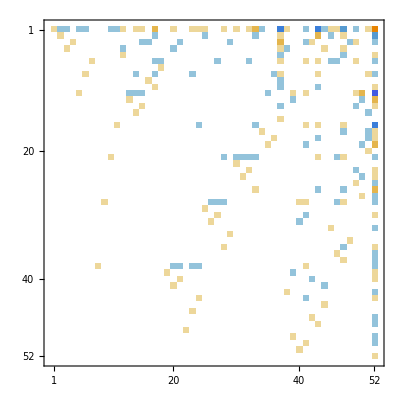

```mathematica
rmat=  Map[
Table[Coefficient[#[[2]],t],{t,randomSyms}]&,
randomfullsol];MatrixPlot[rmat]
```

```mathematica
MatrixRank[rmat]
```

52

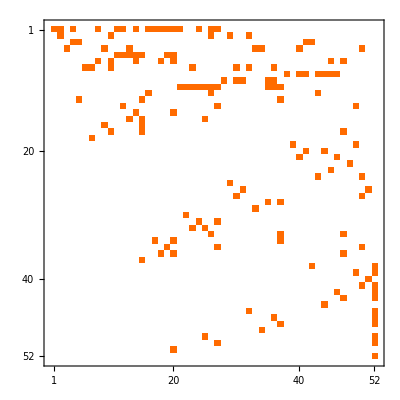

```mathematica
Inverse[rmat]//MatrixPlot
```